```mathematica
Generating a 3-mode Quantum Transducer from Langevin Equations
```

```mathematica
Preliminaries
```

```mathematica
n=6;
Id[n_]:=IdentityMatrix[n]
mJn[n_]:=ArrayFlatten[IdentityMatrix[n]⊗({{0, 1}, {-1, 0}})] ;
mJ = mJn[n];
sympQ[mS_]:=1-Norm[mSᵀ.mJ.mS-mJ];

rSymMat[{a_,b_},c_]:=(UpperTriangularize[#]+UpperTriangularize[#,1]ᵀ)&@RandomReal[{a,b},{c,c}];
rSympMat[a_,b_, n_]:=Id[2n]-Inverse[(mJn[n].rSymMat[{a,b},2n]+1/2 Id[2n])]; 
randomLocal[a_, b_] := ArrayFlatten[({{rSympMat[a,b, 1], 0, 0, 0, 0, 0}, {0, rSympMat[a,b, 1], 0, 0, 0, 0}, {0, 0, rSympMat[a,b, 1], 0, 0, 0}, {0, 0, 0, rSympMat[a,b, 1], 0, 0}, {0, 0, 0, 0, rSympMat[a,b, 1], 0}, {0, 0, 0, 0, 0, rSympMat[a,b, 1]}})];
```

```mathematica
Chop[N[Re[S/.ω -> 560000]], 10^-5] // MatrixForm
```

(0.48969 | -0.985424 | -0.0000169049 | -0.0000362923 | 0.0486622 | -0.0551335 | -0.171012 | 0.3404 | -0.0142001 | -0.00379268 | -0.0975646 | 0.247813
0.985424 | 0.48969 | 0.0000362923 | -0.0000169049 | 0.0551335 | 0.0486622 | 0.3404 | 0.171012 | -0.00379268 | 0.0142001 | 0.247813 | 0.0975646
-0.0000169049 | -0.0000362923 | 1. | 0 | -0.0000121859 | -0.0000253411 | 0 | 0.0000178756 | 0 | 0 | 0 | 0.0000130221
0.0000362923 | -0.0000169049 | 0 | 1. | 0.0000253411 | -0.0000121859 | 0.0000178756 | 0 | 0 | 0 | 0.0000130221 | 0
0.0486622 | -0.0551335 | -0.0000121859 | -0.0000253411 | 0.430656 | -0.956976 | -0.123042 | 0.237577 | -0.00993965 | -0.00278634 | -0.0706609 | 0.173191
0.0551335 | 0.0486622 | 0.0000253411 | -0.0000121859 | 0.956976 | 0.430656 | 0.237577 | 0.123042 | -0.00278634 | 0.00993965 | 0.173191 | 0.0706609
0.171012 | 0.3404 | 0 | 0.0000178756 | 0.123042 | 0.237577 | 0.458969 | -0.257847 | 0.0055341 | 0.0531037 | 0.967799 | 0.00870222
0.3404 | -0.171012 | 0.0000178756 | 0 | 0.237577 | -0.123042 | 0.257847 | 0.458969 | -0.0531037 | 0.0055341 | -0.00870222 | 0.967799
0.0142001 | -0.00379268 | 0 | 0 | 0.00993965 | -0.00278634 | 0.0055341 | 0.0531037 | 0.998037 | 0.0006217 | 0.00720815 | 0.0366248
-0.00379268 | -0.0142001 | 0 | 0 | -0.00278634 | -0.00993965 | -0.0531037 | 0.0055341 | -0.0006217 | 0.998037 | -0.0366248 | 0.00720815
0.0975646 | 0.247813 | 0 | 0.0000130221 | 0.0706609 | 0.173191 | 0.967799 | 0.00870222 | 0.00720815 | 0.0366248 | -0.300295 | -0.278634
0.247813 | -0.0975646 | 0.0000130221 | 0 | 0.173191 | -0.0706609 | -0.00870222 | 0.967799 | -0.0366248 | 0.00720815 | 0.278634 | -0.300295)

```mathematica
H = 1/2({{Subscript[Δ, o], Subscript[g, om], 0, 0, Subscript[g, om], 0}, {Subscript[g, om], Subscript[ω, m], Subscript[g, μm], Subscript[g, om], 0, Subscript[g, μm]}, {0, Subscript[g, μm], Subscript[Δ, μ], 0, Subscript[g, μm], 0}, {0, Subscript[g, om], 0, Subscript[Δ, o], Subscript[g, om], 0}, {Subscript[g, om], 0, Subscript[g, μm], Subscript[g, om], Subscript[ω, m], Subscript[g, μm]}, {0, Subscript[g, μm], 0, 0, Subscript[g, μm], Subscript[Δ, μ]}});           (* or H := ({{A, B}, {B^†, P}}) *)
a⃗ = {Subscript[a, o], Subscript[a, m], Subscript[a, μ], SuperDagger[Subscript[a, o]], SuperDagger[Subscript[a, m]], SuperDagger[Subscript[a, μ]]};
SuperDagger[a⃗]= {SuperDagger[(Subscript[a, o])],SuperDagger[(Subscript[a, m])],SuperDagger[(Subscript[a, μ])],Subscript[a, o],Subscript[a, m],Subscript[a, μ]};
```

```mathematica
Simplify[SuperDagger[a⃗].H.a⃗] (* this ignores commutativity though *)
```

```mathematica
Theory
```

References:"Cavity Optomechanics" (https: //arxiv.org/abs/1303.0733) and KL paper (https: //www.nature.com/articles/nphys2911)

Linearized Hamiltonian:H=Δ_o ((a_o)^† a_o+1/2)+Δ_μ ((a_μ)^† a_μ+1/2)+ω_m ((a_m)^† a_m+1/2)+g_om (a_o+(a_o)^†) (a_m+(a_m)^†)+g_μm (a_μ+(a_μ)^†) (a_m+(a_m)^†)   
Langevin Eq: d/dt (a
a^†)= I [(a | a^†)H(a
a^†), (a
a^†)] - 1/2(κ | 0
0 | κ)(a
a^†)+(√κ | 0
0 | √κ)(A_in
A_in^†) (*1mode example *)
Fourier Transform: â[ω] ∝∫â(t) e^(-I ω t)dt       and     (â[-ω])^† ∝∫â (t)^† e^(-I ω t)dt
Langevin → (I ω | □
□ | Iω)(a[ω]
a[-ω]^†)= I(-A^⋆-P | -B^†
B^ᵀ | A+P^⋆)(a[ω]
a[-ω]^†)- 1/2(κ | 0
0 | κ)(a[ω]
a[-ω]^†) + (√κ | 0
0 | √κ)(A_in[ω]
A_in[-ω]^†)
Thus →    T(a[ω]
a[-ω]^†) = Y(A_in[ω]
A_in[-ω]^†); then extend this to a[-ω] and a[ω]^†modes to get full matrixffff
Input Output relation: A_out[ω] = A_in[ω] - √κ a[ω]; gives matrix equations (A⃗)_out[ω] = (A⃗)_in[ω] - W(M^-1 W  (A⃗)_in)= S_complex(A⃗)_in

```mathematica
Setup and Initialization
```

```mathematica
T[ω_] := I({{ω, 0, 0, 0, 0, 0}, {0, ω, 0, 0, 0, 0}, {0, 0, ω, 0, 0, 0}, {0, 0, 0, ω, 0, 0}, {0, 0, 0, 0, ω, 0}, {0, 0, 0, 0, 0, ω}}) - I({{- Subscript[Δ, o]+I Subscript[κ, o]/2, -Subscript[g, om], 0, 0, -Subscript[g, om]/2, 0}, {-Subscript[g, om], - ωm+I Subscript[κ, m]/2, -Subscript[g, μm], -Subscript[g, om]/2, 0, -Subscript[g, μm]/2}, {0, -Subscript[g, μm], - Subscript[Δ, μ]+I Subscript[κ, μ]/2, 0, -Subscript[g, μm]/2, 0}, {0, Subscript[g, om]/2, 0, Subscript[Δ, o]+ I Subscript[κ, o]/2, Subscript[g, om], 0}, {Subscript[g, om]/2, 0, Subscript[g, μm]/2, Subscript[g, om], ωm+I Subscript[κ, m]/2, Subscript[g, μm]}, {0, Subscript[g, μm]/2, 0, 0, Subscript[g, μm], Subscript[Δ, μ]+ I Subscript[κ, μ]/2}})
```

```mathematica
M[ω_] := ({{T[ω], 0}, {0, T[-ω]}}) // ArrayFlatten
```

```mathematica
Y = ({{√Subscript[κ, o], 0, 0, 0, 0, 0}, {0, √Subscript[κ, m], 0, 0, 0, 0}, {0, 0, √Subscript[κ, μ], 0, 0, 0}, {0, 0, 0, √Subscript[κ, o], 0, 0}, {0, 0, 0, 0, √Subscript[κ, m], 0}, {0, 0, 0, 0, 0, √Subscript[κ, μ]}});
W = ({{Y, 0}, {0, Y}}) // ArrayFlatten;
```

```mathematica
Setting values
```

```mathematica
{Subscript[Δ, o], ωm, Subscript[Δ, μ], Subscript[κ, o], Subscript[κ, μ]} = {730, 560, 650, 1650, 1590}*1000 (*kHz->Hz*)
{Subscript[κ, m], Subscript[g, om],Subscript[g, μm]} = {4,- 34000,- 23000}  (*Hz*)
```

{730000,560000,650000,1650000,1590000}

{4,-34000,-23000}

```mathematica
Finding Scattering Matrices
```

```mathematica
(SComplex= Id[12] - W.Inverse[M[ω]].W );
```

We want to change from basis A to basis B
(A) ao[+ω], am[+ω],aμ[+ω],(ao[-ω])^†,(am[-ω])^†,(aμ[-ω])^†,ao[-ω],am[-ω],aμ[-ω], ...
(B) qo[+ω], po[+ω],qm[+ω], pm[+ω], qμ[+ω], pμ[+ω],qo[-ω], po[-ω], ...

```mathematica
U = 1/(√2)({{1, I, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, I, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, I, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 1, -I, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, -I, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, -I}, {0, 0, 0, 0, 0, 0, 1, I, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, I, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, I}, {1, -I, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 1, -I, 0, 0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 1, -I, 0, 0, 0, 0, 0, 0}});
```

```mathematica
(S = Inverse[U].SComplex.U);
```

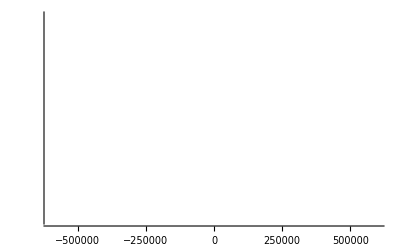

```mathematica
Plot[N[sympQ[S/.{ω->x}]] , {x, -600000, 600000}](* evaluate this numerically? *)
```

### Symplectic Decoupling Algorithm

### Part 1: Decouple the first quadrature

Note that “⟦{1,7,2,8,3,9,4,10,5,11,6,12}, {1,7,2,8,3,9,4,10,5,11,6,12}⟧” converts from “qqpp” → “qpqp”; meanwhile “⟦{1,3,5,7,9,11,2,4,6,8,10,12}, {1,3,5,7,9,11,2,4,6,8,10,12}⟧” converts “qpqp” → “qqpp”.

```mathematica
mR1 = randomLocal[-3, 3];
mS = S/. {ω-> 560000};

(* Tabular representations of column vector cv and row vectow rv in qpqp basis *)
{c, r} = {9,9}; (*we are going to rotate column c -> row r*)
cv=Table[{mS⟦i,c⟧,mS⟦i+1,c⟧},{i,1,2n, 2}];
rv=Table[{mS⟦r,i⟧,mS⟦r,i+1⟧},{i,1,2n, 2}];

ncv=Norm/@cv; (*list of norms of cv*)
nrv=Norm/@rv;(*list of norms of rv*)
mL=Table[(({{rv⟦i,1⟧, -rv⟦i,2⟧}, {rv⟦i,2⟧, rv⟦i,1⟧}})/nrv⟦i⟧).({{nrv⟦i⟧/ncv⟦i⟧, 0}, {0, ncv⟦i⟧/nrv⟦i⟧}}).(({{cv⟦i,1⟧, cv⟦i,2⟧}, {-cv⟦i,2⟧, cv⟦i,1⟧}})/ncv⟦i⟧),{i,1,n}]; 
(*List of local symplectic operations for all modes*)
```

```mathematica
mSL1qq=ArrayFlatten[({{DiagonalMatrix[mL⟦;;,1,1⟧], DiagonalMatrix[mL⟦;;,1,2⟧]}, {DiagonalMatrix[mL⟦;;,2,1⟧], DiagonalMatrix[mL⟦;;,2,2⟧]}})]; (*this gives a result in qqpp*)
mSL1 = mSL1qq⟦{1,7,2,8,3,9,4,10,5,11,6,12}, {1,7,2,8,3,9,4,10,5,11,6,12}⟧; (*convert to qpqp basis*)
sympQ[mSL1]
```

1

```mathematica
Chop[N[Re[mS1 = mS.mJ.mSL1.mS]], 10^-5] // MatrixForm
```

(-1.00982 | 0.241103 | 0.0000220177 | 0.0000610334 | -0.0181312 | 0.0416504 | 0.161852 | -0.165808 | 0 | 0 | 0.102217 | -0.125672
-0.241103 | -1.00982 | -0.0000610334 | 0.0000220177 | -0.0416504 | -0.0181312 | -0.165808 | -0.161852 | 0 | 0 | -0.125672 | -0.102217
0.0000220177 | 0.0000610334 | -0.772212 | 0.635364 | 0.0000159905 | 0.0000426721 | 0.0000469441 | -0.0000179585 | 0 | 0 | 0.0000315511 | -0.0000154697
-0.0000610334 | 0.0000220177 | -0.635364 | -0.772212 | -0.0000426721 | 0.0000159905 | -0.0000179585 | -0.0000469441 | 0 | 0 | -0.0000154697 | -0.0000315511
-0.0181312 | 0.0416504 | 0.0000159905 | 0.0000426721 | -0.990866 | 0.235689 | 0.115099 | -0.115044 | 0 | 0 | 0.0728717 | -0.0873731
-0.0416504 | -0.0181312 | -0.0000426721 | 0.0000159905 | -0.235689 | -0.990866 | -0.115044 | -0.115099 | 0 | 0 | -0.0873731 | -0.0728717
-0.161852 | -0.165808 | -0.0000469441 | -0.0000179585 | -0.115099 | -0.115044 | 0.0818211 | -0.854173 | 0 | 0 | -0.557452 | -0.181969
-0.165808 | 0.161852 | -0.0000179585 | 0.0000469441 | -0.115044 | 0.115099 | 0.854173 | 0.0818211 | 0 | 0 | 0.181969 | -0.557452
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0 | 0
-0.102217 | -0.125672 | -0.0000315511 | -0.0000154697 | -0.0728717 | -0.0873731 | -0.557452 | -0.181969 | 0 | 0 | 0.34472 | -0.759269
-0.125672 | 0.102217 | -0.0000154697 | 0.0000315511 | -0.0873731 | 0.0728717 | 0.181969 | -0.557452 | 0 | 0 | 0.759269 | 0.34472)

```mathematica
sympQ[S.S /. ω -> 100000]
```

1.

```mathematica
N[mSL1.Transpose[mSL1]]// MatrixForm
```

(1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.)

```mathematica
Eigenvalues[mSL1.Transpose[mSL1]]
```

{1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Re[mS1]// MatrixForm
```

(-0.456673 | 0.666106 | -0.0873579 | 0.318804 | -0.429651 | 0.24676 | -0.0283984 | 0.522992 | -0.420216 | -0.433992 | 0.621651 | -0.216297
-1.33004 | -1.3134 | -0.0631037 | 0.262365 | -0.57084 | 1.47762 | 0.843019 | 0.856564 | -0.320732 | -1.29292 | 1.08993 | -0.689335
1.11402 | -0.335141 | 2.33952 | -0.179364 | 1.19084 | -0.661634 | 0.0420638 | -2.52708 | 1.39273 | 2.10637 | 0.950205 | -1.17924
-0.172381 | 0.478718 | -0.249111 | 1.49992 | -0.458254 | 0.55123 | -0.945713 | -0.719208 | -0.985398 | -0.39686 | 1.09654 | 0.312838
-5.37865 | 0.198391 | -3.79485 | -0.390827 | -3.81872 | 2.93507 | 2.56732 | 7.50538 | -2.46011 | -8.03147 | -2.03628 | 0.463705
1.68545 | -0.103108 | 0.99901 | 0.559721 | 0.434033 | -0.559845 | -0.848342 | -1.52779 | 0.0434236 | 2.80071 | 0.465567 | -0.549072
-1.86746 | -0.2028 | -2.47452 | -0.1749 | -1.52696 | 1.19342 | 0.899573 | 5.66644 | -1.06783 | -2.77614 | -1.92742 | -0.159665
0.261456 | -0.0791921 | -0.050674 | 0.583085 | 0.527749 | 0.080553 | -1.31976 | -0.951537 | -0.567626 | 0.520035 | 0.203902 | 0.488212
-1.01114 | 0.296141 | -0.881817 | -1.41638 | 0.592155 | -0.84603 | 0.65057 | 1.05251 | 1.05801 | -1.85822 | -1.87163 | 1.23437
3.68645 | -0.447619 | 3.43796 | 0.848566 | 2.63468 | -1.25756 | -1.8629 | -6.50513 | 1.73376 | 6.63151 | 2.72317 | -1.23311
-0.843548 | -0.0124543 | -0.100695 | 0.964237 | -0.608894 | 0.713791 | 0.472903 | 0.306642 | -0.158688 | -0.98533 | 1.50828 | -1.04042
1.23204 | 0.0456373 | 1.10422 | 0.737377 | 0.843774 | -0.249177 | -0.616181 | -2.07289 | 0.649508 | 1.61155 | 2.12351 | -0.497151)